We consider the master equation 

dρ/dt=ℒ(ρ) = -i[H,ρ] + D[L]ρ

with a single jump operator L.

The stochastic master equation for the quantum diffusion unravelling reads 

dρ=dt (-i[H,ρ]+D[L]ρ) + dW ( L e^-iϕ ρ + ρ L†e^iϕ - ρ⟨L e^-iϕ+L† e^iϕ⟩)

And the current measured in the output reads 

I_d=⟨L e^-iϕ+L† e^iϕ⟩ + dW/dt

### Example: L=√Γ σ_z

In this case the current will be 

I_d= 2 √Γ⟨σ_z⟩ + dW/dt

```mathematica
Clear[H];

H[Δ_,Ω_] := Δ/2 σz+Ω σx;
L = √Γ σz;

dt = 0.001;
tf = 5;
Δ = 0;
Γ = 1.0;
(* Strong Rabi drive *)
Ω = 8.0;
sim1 = QuantumDiffusion[ψ0={1,0},H[Δ,Ω],L,dt,tf];

(* Weak Rabi drive *)
Ω = 0.4;
sim2 = QuantumDiffusion[ψ0={1,0},H[Δ,Ω],L,dt,6tf];
```

0h : 0m : 0s

0h : 0m : 1s

```mathematica
sim1
```

```mathematica
Keys[sim1]
```

{dt,tf,nsteps,state,I,xave,f}

```mathematica
rasta[ListLinePlot[{1/(2 √Γ)sim1["xave"],1/(2 √Γ)sim2["xave"]},
DataRange->{dt,tf},
PlotStyle->{Black,Red},
AspectRatio->1/3,
ImageSize->900,
PlotRange->{-1,1},
PlotLabel->"Population of the qubit ⟨σ_z⟩"
],100,500]
```

-Graphics-

```mathematica
Manipulate[Plot[szExact/.{Γ->1,Ω->ΩΩ},{t,0,8},
PlotLabel->"Ω = "<>ToString@ΩΩ,
PlotRange->{-1,1}
]
,{{ΩΩ,1,"Ω"},0,4}]
```

```mathematica
{rasta@ListLinePlot[sim1["I"],PlotRange->All,DataRange->{dt,tf},
PlotLabel->"Raw output current I_d"
],
rasta@ListLinePlot[sim2["I"],PlotRange->All,DataRange->{dt,tf},
PlotLabel->"Raw output current I_d"
]}
```

{-Graphics-,-Graphics-}

```mathematica
rasta[ListLinePlot[{1/(2 √Γ)sim1["xave"],LowpassFilter[sim1["I"]/(2 √Γ),0.7]},
DataRange->{dt,tf},
PlotStyle->{Black,Red},
AspectRatio->1/3,
ImageSize->900,
PlotRange->All,
PlotLabel->"Population of the qubit ⟨σ_z⟩ for Ω = 8"
],100,700]
```

-Graphics-

```mathematica
rasta[ListLinePlot[{1/(2 √Γ)sim1["xave"],butter[sim1["I"]/(2 √Γ),0.01](*LowpassFilter[sim1["I"]/(2 √Γ),0.01]*)},
DataRange->{dt,tf},
PlotStyle->{Black,Red},
AspectRatio->1/3,
ImageSize->900,
PlotRange->{-2,2},
PlotLabel->"Population of the qubit ⟨σ_z⟩ for Ω = 8"
],100,700]
rasta[ListLinePlot[{1/(2 √Γ)sim2["xave"],(*,LowpassFilter[sim2["I"]/(2 √Γ),0.02],BandpassFilter[sim2["I"]/(2 √Γ),{0.02,0.02}],*)butter[sim2["I"]/(2 √Γ),0.01]},
DataRange->{dt,tf},
PlotStyle->{Black,Red,Blue,Green},
AspectRatio->1/3,
ImageSize->900,
PlotRange->All,
PlotLabel->"Population of the qubit ⟨σ_z⟩ for Ω = 0.5"
],100,700]
```

-Graphics-

-Graphics-

#### How this reflects the unconditional dynamics

```mathematica
Clear[Γ,Δ,Ω];
L = √Γ σz;
ℒ = Liouvillian[H[0,Ω],{L}]//Normal//cf;
ρ0 = out[ψ0,ψ0];
szExact = Tr[σz.Unvec@MatrixExp[ℒ t,Vec[ρ0]]]//cf
```

ⅇ^(-t Γ) (Cosh[t √(Γ^2-4 Ω^2)]+(Γ Sinh[t √(Γ^2-4 Ω^2)])/(√(Γ^2-4 Ω^2)))

```mathematica
Manipulate[Plot[szExact/.{Γ->1,Ω->ΩΩ},{t,0,8},
PlotLabel->"Ω = "<>ToString@ΩΩ,
PlotRange->{-1,1}
]
,{{ΩΩ,1,"Ω"},0,4}]
```

```mathematica
Γ=1.0;
rasta[Show[
ListLinePlot[{1/(2 √Γ)sim1["xave"]},
DataRange->{dt,tf},
PlotStyle->Directive[Black,Thin],
AspectRatio->1/3,
ImageSize->900,
PlotRange->{-1,1},
PlotLabel->"Population of the qubit ⟨σ_z⟩"
],
Plot[szExact/.{Γ->1,Ω->4},{t,0,tf},PlotStyle->Directive[Red,Thick]]

],100,900]
```

-Graphics-

```mathematica
Γ=1.0;
rasta[Show[
ListLinePlot[{1/(2 √Γ)sim2["xave"]},
DataRange->{dt,tf},
PlotStyle->Directive[Black,Thin],
AspectRatio->1/3,
ImageSize->900,
PlotRange->{-1,1},
PlotLabel->"Population of the qubit ⟨σ_z⟩"
],
Plot[szExact/.{Γ->1,Ω->0.4},{t,0,tf},PlotStyle->Directive[Red,Thick]]

],100,900]
```

-Graphics-

#### Two-point current correlation function and power spectrum

```mathematica
Clear[Γ,Ω,Δ];

Clear[H];
H[Δ_,Ω_] := Δ/2 σz+Ω σx;
L = √Γ σz;

ℒ = Liouvillian[H[0,Ω],L]//Normal//cf;
ρ = SteadyState[ℒ];
```

```mathematica
F=FCSTwoPointFunction[t,ρ,ℒ,L,1,"Diffusion"]//cf
```

4 ⅇ^(-t Γ) Γ (Cosh[t √(Γ^2-4 Ω^2)]+(Γ Sinh[t √(Γ^2-4 Ω^2)])/(√(Γ^2-4 Ω^2)))

```mathematica
S=FCSPowerSpectrum[ω,ρ,ℒ,L,1,"Diffusion"]//cf
```

1+(64 Γ^2 Ω^2)/(4 Γ^2 ω^2+(ω^2-4 Ω^2)^2)

```mathematica
Eigenvalues[H[0,Ω]]
```

{-Ω,Ω}

```mathematica
F
```

4 ⅇ^(-t Γ) Γ (Cosh[t √(Γ^2-4 Ω^2)]+(Γ Sinh[t √(Γ^2-4 Ω^2)])/(√(Γ^2-4 Ω^2)))

```mathematica
S
```

1+(64 Γ^2 Ω^2)/(4 Γ^2 ω^2+(ω^2-4 Ω^2)^2)

```mathematica
Γ
```

Γ

```mathematica
Ω
```

Ω

```mathematica
Manipulate[
Row[{
Plot[F/.{Γ->1,Ω->ΩΩ},{t,0,8},
GridLines->{{-2ΩΩ,2ΩΩ},None},
GridLinesStyle->Directive[Black,Dashed]
],
Plot[S/.{Γ->1,Ω->ΩΩ},{ω,-10,10},
GridLines->{{-2ΩΩ,2ΩΩ},None},
GridLinesStyle->Directive[Black,Dashed]
]
}]
,{{ΩΩ,1,"Ω"},0,4}]
```

```mathematica
Γ = 1;
Ω = 4.0;
sim1long = QuantumDiffusion[ψ0={1,0},H[Δ,Ω],L,dt,50tf];
```

0h : 0m : 2s

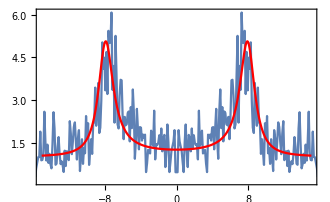

```mathematica
Show[
ListLinePlot[PowerSpectrum[sim1long["I"],dt,5],PlotRange->{{-15,15},All}],
Plot[S,{ω,-15,15},PlotStyle->Red]
]
```

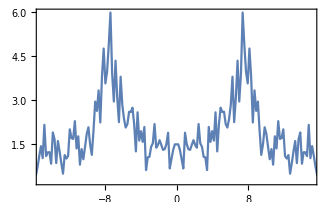

```mathematica
ListLinePlot[PowerSpectrum[sim1long["I"],dt,8],PlotRange->{{-15,15},All}]
```